```mathematica
pdfordk[x_,n_,k_]:=n Binomial[n-1,k-1](1-x)^((n-1)-(k-1))x^(k-1);
```

```mathematica
Refine[∫_0^x pdfordk[y,n,k]ⅆy,n>0&&k>0&&x≤1]
```

n Beta[x,k,1-k+n] Binomial[-1+n,-1+k]

```mathematica
cdfordk[x_,n_,k_]:=n  Binomial[n-1,k-1]Beta[x,k,n-k+1];
```

```mathematica
delta[x_,n_,dnk_:1]:=∑_(k=n-dnk)^(n-1) cdfordk[x,n,k]-cdfordk[x,n,n];
```

```mathematica
Solve[D[delta[x,n,1],x]==0,x]
```

{{x→(-1+n)/n}}

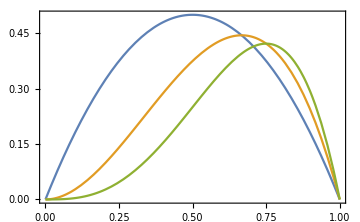

```mathematica
Plot[{delta[x,2],delta[x,3],delta[x,4]},{x,0,1},ImageSize->Medium,PlotRange->All,Frame->True]
```

## n = 2

### First round

```mathematica
draws2=RandomReal[{0,1},{10000000,2}];
```

```mathematica
maxs2=Map[Max,draws2];
```

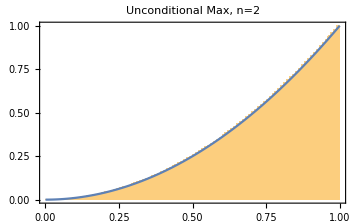

```mathematica
Show[Histogram[maxs2,{10^-2},"CDF",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Unconditional Max, n=2"],
Plot[cdfordk[x,2,2],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotLabel->"Unconditional Max, n=2"]]
```

### Second round

```mathematica
fmax2u[list_]:=Max[Rest[list]];
```

```mathematica
max1u=Map[fmax2u,draws2];
```

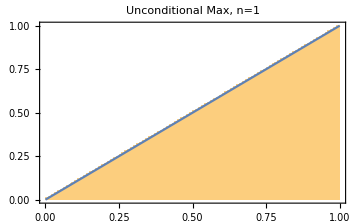

```mathematica
Show[Histogram[max1u,{10^-2},"CDF",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Unconditional Max, n=1"],
Plot[cdfordk[x,1,1],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotLabel->"Unconditional Max, n=1"]]
```

```mathematica
maxfirst2=MapThread[(First[#1]==#2)&,{draws2,maxs2}];
```

```mathematica
Tally[maxfirst2]
```

{{False,5000114},{True,4999886}}

```mathematica
maxnotfirst2=MapThread[(First[#1]≠#2)&,{draws2,maxs2}];
```

```mathematica
Tally[maxnotfirst2]
```

{{True,5000114},{False,4999886}}

```mathematica
max1c=Pick[max1u,maxnotfirst2];
```

```mathematica
max1cn=Pick[max1u,maxfirst2];
```

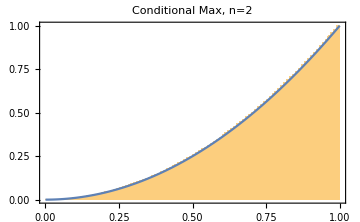

```mathematica
Show[Histogram[max1c,{10^-2},"CDF",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Conditional Max, n=2"],
Plot[cdfordk[x,2,2],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotLabel->"Unconditional Max, n=2"]]
```

```mathematica
maxnotfirstk2=MapThread[((First[#1]≠#2)&&First[#1]<0.5)&,{draws2,maxs2}];
```

```mathematica
Tally[maxnotfirstk2]
```

{{True,3748429},{False,6251571}}

```mathematica
max1ck=Pick[max1u,maxnotfirstk2];
```

```mathematica
Expectation[x2,x1\[Distributed]UniformDistribution[]&&x2\[Distributed]UniformDistribution[]]
```

1/2

```mathematica
Assuming[0<z<1,Probability[x2<z&&x1<0.5&&x2>x1,x1\[Distributed]UniformDistribution[]&&x2\[Distributed]UniformDistribution[]]]
```

Piecewise[{{-0.125+0.5 z, z>0.5}, {0.5 z^2, True}}]

```mathematica
Assuming[0<z<1,Probability[x2<z&&x1<0.5&&x2>x1,x1\[Distributed]UniformDistribution[]&&x2\[Distributed]UniformDistribution[]]/Probability[x1<0.5&&x2>x1,x1\[Distributed]UniformDistribution[]&&x2\[Distributed]UniformDistribution[]]]
```

2.66667 (Piecewise[{{-0.125+0.5 z, z>0.5}, {0.5 z^2, True}}])

```mathematica
cdfx2[z_]:=2.6666666666666665 Piecewise[{{-0.125+0.5 z, z>0.5}, {0.5 z^2, True}}]
```

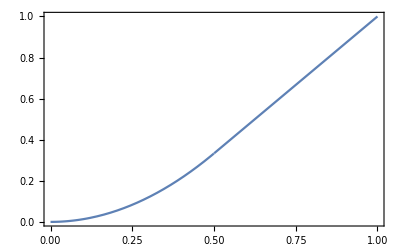

```mathematica
Plot[cdfx2[z],{z,0,1},Frame->True,PlotRange->All]
```

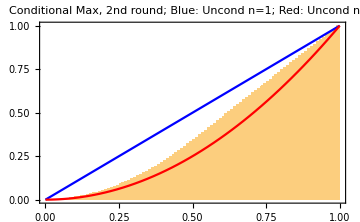

```mathematica
Show[Histogram[max1ck,{10^-2},"CDF",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Conditional Max, 2nd round; Blue: Uncond n=1; Red: Uncond n=2"],
Plot[cdfordk[x,1,1],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotStyle->Blue],
Plot[cdfordk[x,2,2],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotStyle->Red]]
```

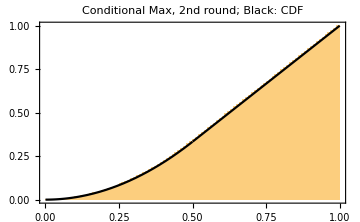

```mathematica
Show[Histogram[max1ck,{10^-2},"CDF",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Conditional Max, 2nd round; Black: CDF"],
Plot[cdfx2[x],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotStyle->Black]]
```

```mathematica
maxwhateverk2=MapThread[(First[#1]<0.5)&,{draws2,maxs2}];
```

```mathematica
Tally[maxwhateverk2]
```

{{True,4999416},{False,5000584}}

```mathematica
max1cwtvk=Pick[max1u,maxwhateverk2];
```

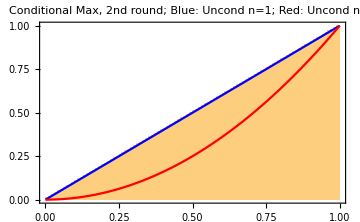

```mathematica
Show[Histogram[max1cwtvk,{10^-2},"CDF",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Conditional Max, 2nd round; Blue: Uncond n=1; Red: Uncond n=2"],
Plot[cdfordk[x,1,1],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotStyle->Blue],
Plot[cdfordk[x,2,2],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotStyle->Red]]
```

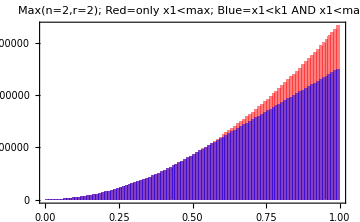

```mathematica
Histogram[{max1c,max1ck},{10^-2},"CumulativeCount",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Max(n=2,r=2); Red=only x1<max; Blue=x1<k1 AND x1<max",ChartStyle->{Red,Blue}]
```

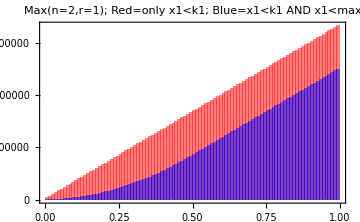

```mathematica
Histogram[{max1cwtvk,max1ck},{10^-2},"CumulativeCount",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Max(n=2,r=1); Red=only x1<k1; Blue=x1<k1 AND x1<max",ChartStyle->{Red,Blue}]
```

```mathematica
Histogram3D[Transpose[{Pick[Map[First,draws2],maxwhateverk2],max1cwtvk}],{10^-2},"CumulativeCount",ImageSize->Large,PlotLabel->"Max(n=2,r=1): x1 vs max{x2)|x1<k1",AxesLabel->{"x1","max{x2)|x1<k1"}]
```

-Graphics3D-

```mathematica
Histogram3D[Transpose[{Pick[Map[First,draws2],maxnotfirst2],max1c}],{10^-2},"CumulativeCount",ImageSize->Large,PlotLabel->"Max(n=2,r=1): x1 vs max{x2)|x1<max",AxesLabel->{"x1","max{x2)|x1<max"}]
```

-Graphics3D-

```mathematica
Histogram3D[Transpose[{Pick[Map[First,draws2],maxnotfirstk2],max1ck}],{10^-2},"CumulativeCount",ImageSize->Large,PlotLabel->"Max(n=2,r=1): x1 vs max{x2)|(x1<k1 AND x1<max)",AxesLabel->{"x1","max{x2)|(x1<k1 AND x1<max)"}]
```

-Graphics3D-

```mathematica
fmin2u[list_]:=Min[Rest[list]];
```

```mathematica
min1u=Map[fmin2u,draws2];
```

```mathematica
min1ck=Pick[min1u,maxnotfirstk2];
```

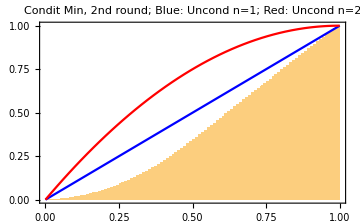

```mathematica
Show[Histogram[min1ck,{10^-2},"CDF",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Condit Min, 2nd round; Blue: Uncond n=1; Red: Uncond n=2"],
Plot[cdfordk[x,1,1],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotStyle->Blue],
Plot[cdfordk[x,2,1],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotStyle->Red]]
```

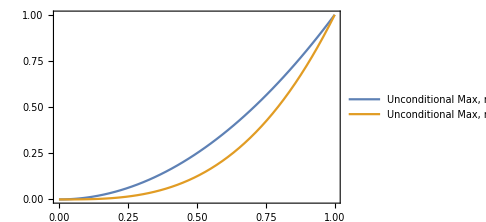

```mathematica
Plot[{cdfordk[x,2,2],cdfordk[x,3,3]},{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotLegends->{"Unconditional Max, n=2", "Unconditional Max, n=3"}]
```

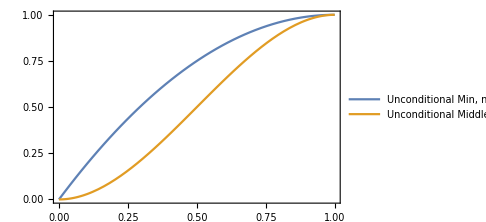

```mathematica
Plot[{cdfordk[x,2,1],cdfordk[x,3,2]},{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotLegends->{"Unconditional Min, n=2", "Unconditional Middle, n=3"}]
```

## n = 3

```mathematica
cdfordk[x,3,3]
```

x^3

### First round

```mathematica
draws3=RandomReal[{0,1},{10000000,3}];
```

```mathematica
maxs3=Map[Max,draws3];
```

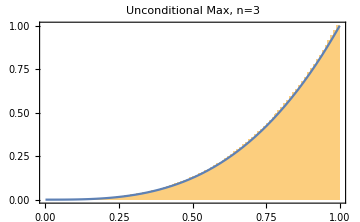

```mathematica
Show[Histogram[maxs3,{10^-2},"CDF",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Unconditional Max, n=3"],
Plot[cdfordk[x,3,3],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotLabel->"Unconditional Max, n=3"]]
```

### Second round

```mathematica
max2u=Map[fmax2u,draws3];
```

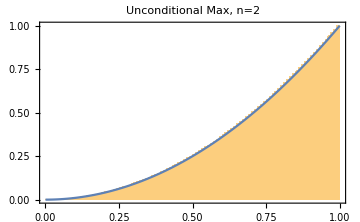

```mathematica
Show[Histogram[max2u,{10^-2},"CDF",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Unconditional Max, n=2"],
Plot[cdfordk[x,2,2],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotLabel->"Unconditional Max, n=2"]]
```

```mathematica
maxfirst=MapThread[(First[#1]==#2)&,{draws3,maxs3}];
```

```mathematica
Tally[maxfirst]
```

{{True,3331678},{False,6668322}}

```mathematica
maxnotfirst=MapThread[(First[#1]≠#2)&,{draws3,maxs3}];
```

```mathematica
Tally[maxnotfirst]
```

{{False,3331678},{True,6668322}}

```mathematica
max2c=Pick[max2u,maxnotfirst];
```

```mathematica
max2cn=Pick[max2u,maxfirst];
```

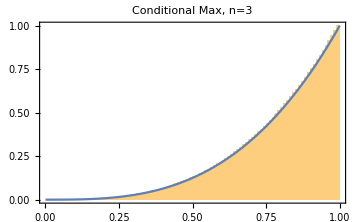

```mathematica
Show[Histogram[max2c,{10^-2},"CDF",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Conditional Max, n=3"],
Plot[cdfordk[x,3,3],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotLabel->"Unconditional Max, n=3"]]
```

```mathematica
maxnotfirstk=MapThread[((First[#1]≠#2)&&First[#1]<0.689897948556636)&,{draws3,maxs3}];
```

```mathematica
Tally[maxnotfirstk]
```

{{False,4192598},{True,5807402}}

```mathematica
max2ck=Pick[max2u,maxnotfirstk];
```

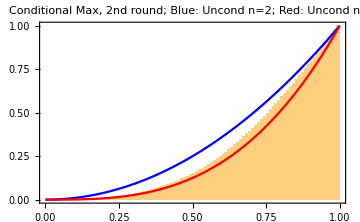

```mathematica
Show[Histogram[max2ck,{10^-2},"CDF",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Conditional Max, 2nd round; Blue: Uncond n=2; Red: Uncond n=3"],
Plot[cdfordk[x,2,2],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotStyle->Blue],
Plot[cdfordk[x,3,3],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotStyle->Red]]
```

```mathematica
maxwhateverk=MapThread[(First[#1]<0.689897948556636)&,{draws3,maxs3}];
```

```mathematica
Tally[maxwhateverk]
```

{{True,6902009},{False,3097991}}

```mathematica
max2cwtvk=Pick[max2u,maxwhateverk];
```

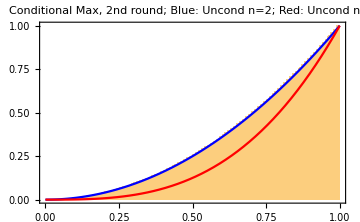

```mathematica
Show[Histogram[max2cwtvk,{10^-2},"CDF",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Conditional Max, 2nd round; Blue: Uncond n=2; Red: Uncond n=3"],
Plot[cdfordk[x,2,2],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotStyle->Blue],
Plot[cdfordk[x,3,3],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotStyle->Red]]
```

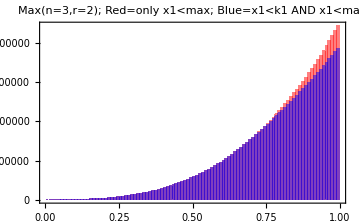

```mathematica
Histogram[{max2c,max2ck},{10^-2},"CumulativeCount",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Max(n=3,r=2); Red=only x1<max; Blue=x1<k1 AND x1<max",ChartStyle->{Red,Blue}]
```

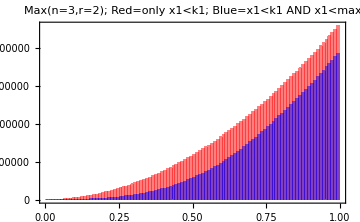

```mathematica
Histogram[{max2cwtvk,max2ck},{10^-2},"CumulativeCount",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Max(n=3,r=2); Red=only x1<k1; Blue=x1<k1 AND x1<max",ChartStyle->{Red,Blue}]
```

```mathematica
Histogram3D[Transpose[{Pick[Map[First,draws3],maxwhateverk],max2cwtvk}],{10^-2},"CumulativeCount",ImageSize->Medium,PlotLabel->"Max(n=3,r=2): x1 vs max{x2,x3)|x1<k1",AxesLabel->{"x1","max{x2,x3)|x1<k1"}]
```

-Graphics3D-

```mathematica
Histogram3D[Transpose[{Pick[Map[First,draws3],maxnotfirst],max2c}],{10^-2},"CumulativeCount",ImageSize->Medium,PlotLabel->"Max(n=3,r=2): x1 vs max{x2,x3)|x1<max",AxesLabel->{"x1","max{x2,x3)|x1<max"}]
```

-Graphics3D-

```mathematica
Histogram3D[Transpose[{Pick[Map[First,draws3],maxnotfirstk],max2ck}],{10^-2},"CumulativeCount",ImageSize->Medium,PlotLabel->"Max(n=3,r=2): x1 vs max{x2,x3)|(x1<k1 AND x1<max)",AxesLabel->{"x1","max{x2,x3)|(x1<k1 AND x1<max)"}]
```

-Graphics3D-

```mathematica
min2u=Map[fmin2u,draws3];
```

```mathematica
min2ck=Pick[min2u,maxnotfirstk];
```

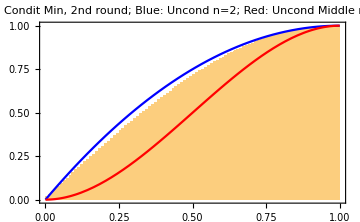

```mathematica
Show[Histogram[min2ck,{10^-2},"CDF",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Condit Min, 2nd round; Blue: Uncond n=2; Red: Uncond Middle n=3"],
Plot[cdfordk[x,2,1],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotStyle->Blue],
Plot[cdfordk[x,3,2],{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotStyle->Red]]
```

```mathematica
Plot[{cdfordk[x,2,2],cdfordk[x,3,3]},{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotLegends->{"Unconditional Max, n=2", "Unconditional Max, n=3"}]
```

-Graphics-

```mathematica
Plot[{cdfordk[x,2,1],cdfordk[x,3,2]},{x,0,1},ImageSize->Medium,PlotRange->{{0,1},All},Frame->True,PlotLegends->{"Unconditional Min, n=2", "Unconditional Middle, n=3"}]
```

-Graphics-

## M (j)

```mathematica
mj[list_]:=FoldList[Max,list];
```

```mathematica
mj[{1,4,2,8}]
```

{1,4,4,8}

```mathematica
mjs3=Map[mj,draws3];
```

```mathematica
mjs3m1=Transpose[mjs3]⟦1⟧;
mjs3m2=Transpose[mjs3]⟦2⟧;
mjs3m3=Transpose[mjs3]⟦3⟧;
```

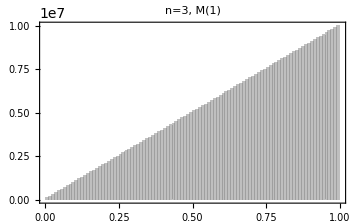

```mathematica
Histogram[{mjs3m1},{10^-2},"CumulativeCount",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"n=3, M(1)",
ChartStyle->{Gray}]
```

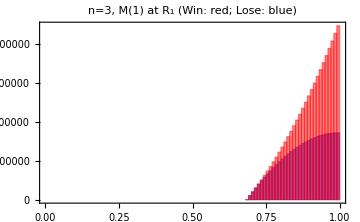

```mathematica
Histogram[{
Pick[mjs3m1,Map[((First[#]>0.689897948556636)&&(First[#]<Max[#]))&,draws3]],
Pick[mjs3m1,Map[((First[#]>0.689897948556636)&&(First[#]==Max[#]))&,draws3]]
},{10^-2},"CumulativeCount",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"n=3, M(1) at R_1 (Win: red; Lose: blue)",
ChartStyle->{Blue,Red}]
```

```mathematica
Assuming[0<Subscript[k, 1]<1&&0<Subscript[k, 2]<1&&Subscript[k, 2]<Subscript[k, 1]&&0<z≤1,
Probability[Max[{Subscript[a, 1]}]≤z&&Max[{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}]≠Subscript[a, 1]&&Subscript[a, 1]>Subscript[k, 1],
Subscript[a, 1]\[Distributed]UniformDistribution[]&&Subscript[a, 2]\[Distributed]UniformDistribution[]&&Subscript[a, 3]\[Distributed]UniformDistribution[]]]
```

Piecewise[{{1/3 (3 z-z^3-3 k_1+k_1^3), z≥1||z>k_1}, {0, True}}]

```mathematica
Assuming[0<Subscript[k, 1]<1&&0<Subscript[k, 2]<1&&Subscript[k, 2]<Subscript[k, 1]&&0<z≤1,
Probability[Max[{Subscript[a, 1]}]≤z&&Max[{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}]==Subscript[a, 1]&&Subscript[a, 1]>Subscript[k, 1],
Subscript[a, 1]\[Distributed]UniformDistribution[]&&Subscript[a, 2]\[Distributed]UniformDistribution[]&&Subscript[a, 3]\[Distributed]UniformDistribution[]]]
```

Piecewise[{{1/3 (z^3-k_1^3), z>k_1}, {0, True}}]

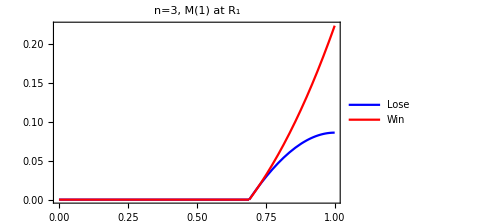

```mathematica
With[{k1=0.689897948556636},Plot[{Piecewise[{{1/3 (3 z-z^3-3 k1+k1^3), z>k1}, {0, True}}],Piecewise[{{1/3 (z^3-k1^3), z>k1}, {0, True}}]},{z,0,1},
ImageSize->Medium,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},
PlotLegends->{"Lose","Win"},PlotLabel->"n=3, M(1) at R_1"]]
```

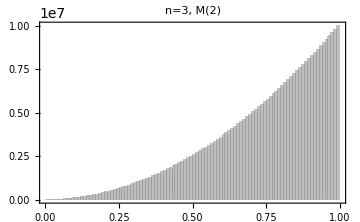

```mathematica
Histogram[{mjs3m2},{10^-2},"CumulativeCount",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"n=3, M(2)",
ChartStyle->{Gray}]
```

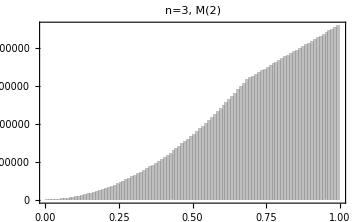

```mathematica
Histogram[{
Pick[mjs3m2,Map[((First[#]<0.689897948556636))&,draws3]]
},{10^-2},"CumulativeCount",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"n=3, M(2)",
ChartStyle->{Gray}]
```

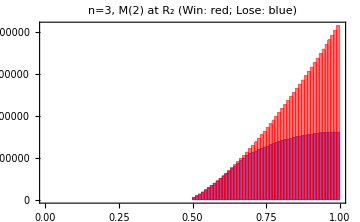

```mathematica
Histogram[{
Pick[mjs3m2,Map[((First[#]<0.689897948556636)&&(#⟦2⟧>0.5)&&(#⟦2⟧<Max[#]))&,draws3]],
Pick[mjs3m2,Map[((First[#]<0.689897948556636)&&(#⟦2⟧>0.5)&&(#⟦2⟧==Max[#]))&,draws3]]
},{10^-2},"CumulativeCount",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"n=3, M(2) at R_2 (Win: red; Lose: blue)",
ChartStyle->{Blue,Red}]
```

```mathematica
Assuming[0<Subscript[k, 1]<1&&0<Subscript[k, 2]<1&&Subscript[k, 2]<Subscript[k, 1]&&0<z<1,
Probability[Max[{Subscript[a, 1],Subscript[a, 2]}]≤z&&Max[{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}]≠Subscript[a, 2]&&Subscript[a, 1]<Subscript[k, 1]&&Subscript[a, 2]>Subscript[k, 2],
Subscript[a, 1]\[Distributed]UniformDistribution[]&&Subscript[a, 2]\[Distributed]UniformDistribution[]&&Subscript[a, 3]\[Distributed]UniformDistribution[]]]
```

Piecewise[{{1/3 (-((-3+z) z^2)-3 z k_2+k_2^3), z<k_1&&z>k_2}, {1/6 (k_1^3+2 k_2^3-3 k_1 ((-2+z) z+2 k_2)), z≥k_1}, {0, True}}]

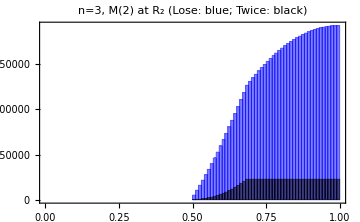

```mathematica
Histogram[{
Pick[mjs3m2,Map[((First[#]<0.689897948556636)&&(#⟦2⟧>0.5)&&(#⟦2⟧<Max[#]))&,draws3]],
Pick[mjs3m2,Map[((First[#]<0.689897948556636)&&(#⟦2⟧>0.5)&&(#⟦1⟧==Max[#]))&,draws3]]
},{10^-2},"CumulativeCount",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"n=3, M(2) at R_2 (Lose: blue; Twice: black)",
ChartStyle->{Blue,Black}]
```

```mathematica
Assuming[0<Subscript[k, 1]<1&&0<Subscript[k, 2]<1&&Subscript[k, 2]<Subscript[k, 1]&&0<z<1,
Probability[Max[{Subscript[a, 1],Subscript[a, 2]}]≤z&&Max[{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}]==Subscript[a, 1]&&Subscript[a, 1]<Subscript[k, 1]&&Subscript[a, 2]>Subscript[k, 2],
Subscript[a, 1]\[Distributed]UniformDistribution[]&&Subscript[a, 2]\[Distributed]UniformDistribution[]&&Subscript[a, 3]\[Distributed]UniformDistribution[]]]
```

Piecewise[{{1/6 (z-k_2)^2 (2 z+k_2), z<k_1&&z>k_2}, {1/6 (k_1-k_2)^2 (2 k_1+k_2), z≥k_1}, {0, True}}]

```mathematica
Assuming[0<Subscript[k, 1]<1&&0<Subscript[k, 2]<1&&Subscript[k, 2]<Subscript[k, 1]&&0<z<1,
Probability[Max[{Subscript[a, 1],Subscript[a, 2]}]≤z&&Max[{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}]==Subscript[a, 3]&&Subscript[a, 1]<Subscript[k, 1]&&Subscript[a, 2]>Subscript[k, 2],
Subscript[a, 1]\[Distributed]UniformDistribution[]&&Subscript[a, 2]\[Distributed]UniformDistribution[]&&Subscript[a, 3]\[Distributed]UniformDistribution[]]]
```

Piecewise[{{1/6 (2 (3-2 z) z^2+3 (-2+z) z k_2+k_2^3), z<k_1&&z>k_2}, {1/6 (-k_1^3+3 k_1^2 k_2+k_2^3-3 k_1 ((-2+z) z+2 k_2)), z≥k_1}, {0, True}}]

```mathematica
Expand[(Subscript[k, 1]-Subscript[k, 2])^2 (2 Subscript[k, 1]+Subscript[k, 2])]
```

2 k_1^3-3 k_1^2 k_2+k_2^3

```mathematica
Expand[ (-Subscript[k, 1]^3+3 Subscript[k, 1]^2 Subscript[k, 2]+Subscript[k, 2]^3-3 Subscript[k, 1] ((-2+1) 1+2 Subscript[k, 2]))]
```

3 k_1-k_1^3-6 k_1 k_2+3 k_1^2 k_2+k_2^3

```mathematica
Expand[Subscript[k, 1]^3+2 Subscript[k, 2]^3-3 Subscript[k, 1] ((-2+1) 1+2 Subscript[k, 2])]
```

3 k_1+k_1^3-6 k_1 k_2+2 k_2^3

```mathematica
Expand[-((-3+z) z^2)-3 z Subscript[k, 2]+Subscript[k, 2]^3]
```

3 z^2-z^3-3 z k_2+k_2^3

```mathematica
Expand[Subscript[k, 1]^3+2 Subscript[k, 2]^3-3 Subscript[k, 1] ((-2+z) z+2 Subscript[k, 2])]
```

6 z k_1-3 z^2 k_1+k_1^3-6 k_1 k_2+2 k_2^3

```mathematica
Assuming[0<Subscript[k, 1]<1&&0<Subscript[k, 2]<1&&Subscript[k, 2]<Subscript[k, 1]&&0<z<1,
Probability[Max[{Subscript[a, 1],Subscript[a, 2]}]≤z&&Max[{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}]==Subscript[a, 2]&&Subscript[a, 1]<Subscript[k, 1]&&Subscript[a, 2]>Subscript[k, 2],
Subscript[a, 1]\[Distributed]UniformDistribution[]&&Subscript[a, 2]\[Distributed]UniformDistribution[]&&Subscript[a, 3]\[Distributed]UniformDistribution[]]]
```

Piecewise[{{1/6 (3 z^2 k_1-k_1^3-2 k_2^3), z≥k_1}, {1/3 (z^3-k_2^3), z<k_1&&z>k_2}, {0, True}}]

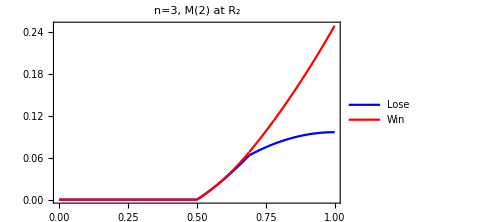

```mathematica
With[{k1=0.689897948556636,k2=0.5},Plot[{Piecewise[{{1/3 (-((-3+z) z^2)-3 z k2+k2^3), z<k1&&z>k2}, {1/6 (k1^3+2 k2^3-3 k1 ((-2+z) z+2 k2)), z≥k1}, {0, True}}],Piecewise[{{1/6 (3 z^2 k1-k1^3-2 k2^3), z≥k1}, {1/3 (z^3-k2^3), z<k1&&z>k2}, {0, True}}]},{z,0,1},
ImageSize->Medium,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},
PlotLegends->{"Lose","Win"},PlotLabel->"n=3, M(2) at R_2"]]
```

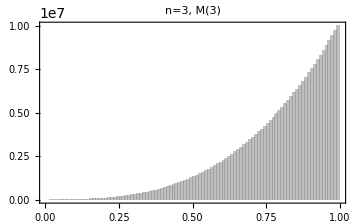

```mathematica
Histogram[{mjs3m3},{10^-2},"CumulativeCount",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"n=3, M(3)",
ChartStyle->{Gray}]
```

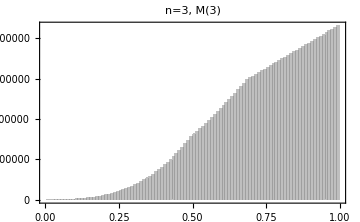

```mathematica
Histogram[{
Pick[mjs3m3,Map[((First[#]<0.689897948556636)&&(#⟦2⟧<0.5))&,draws3]]
},{10^-2},"CumulativeCount",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"n=3, M(3)",
ChartStyle->{Gray}]
```

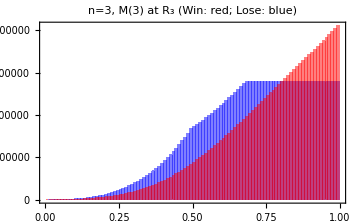

```mathematica
Histogram[{
Pick[mjs3m3,Map[((First[#]<0.689897948556636)&&(#⟦2⟧<0.5)&&(#⟦3⟧<Max[#]))&,draws3]],
Pick[mjs3m3,Map[((First[#]<0.689897948556636)&&(#⟦2⟧<0.5)&&(#⟦3⟧==Max[#]))&,draws3]]
},{10^-2},"CumulativeCount",PlotRange->{{0,1},All},Frame->True,ImageSize->Medium,PlotLabel->"n=3, M(3) at R_3 (Win: red; Lose: blue)",
ChartStyle->{Blue,Red}]
```

```mathematica
Assuming[0<Subscript[k, 1]<1&&0<Subscript[k, 2]<1&&Subscript[k, 2]<Subscript[k, 1]&&0<z<1,
Probability[Max[{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}]≤z&&Max[{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}]≠Subscript[a, 3]&&Subscript[a, 1]<Subscript[k, 1]&&Subscript[a, 2]<Subscript[k, 2],
Subscript[a, 1]\[Distributed]UniformDistribution[]&&Subscript[a, 2]\[Distributed]UniformDistribution[]&&Subscript[a, 3]\[Distributed]UniformDistribution[]]]
```

Piecewise[{{(2 z^3)/3, z<k_1&&z<k_2}, {(2 k_2^3)/3, z<k_1&&z==k_2}, {1/6 (3 z^2 k_2+k_2^3), z<k_1&&z>k_2}, {1/6 (3 k_1^2 k_2+k_2^3), z≥k_1}, {0, True}}]

```mathematica
Assuming[0<Subscript[k, 1]<1&&0<Subscript[k, 2]<1&&Subscript[k, 2]<Subscript[k, 1]&&0<z<1,
Probability[Max[{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}]≤z&&Max[{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}]==Subscript[a, 3]&&Subscript[a, 1]<Subscript[k, 1]&&Subscript[a, 2]<Subscript[k, 2],
Subscript[a, 1]\[Distributed]UniformDistribution[]&&Subscript[a, 2]\[Distributed]UniformDistribution[]&&Subscript[a, 3]\[Distributed]UniformDistribution[]]]
```

Piecewise[{{z^3/3, z<k_1&&z<k_2}, {z k_2^2-(2 k_2^3)/3, z<k_1&&z==k_2}, {1/6 (3 z^2 k_2-k_2^3), z<k_1&&z>k_2}, {-1/6 k_2 (-6 z k_1+3 k_1^2+k_2^2), z≥k_1}, {0, True}}]

```mathematica
Expand[- Subscript[k, 2] (-6 z Subscript[k, 1]+3 Subscript[k, 1]^2+Subscript[k, 2]^2)]
```

6 z k_1 k_2-3 k_1^2 k_2-k_2^3

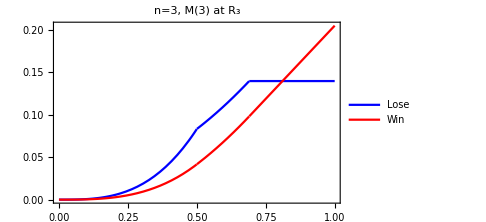

```mathematica
With[{k1=0.689897948556636,k2=0.5},Plot[{Piecewise[{{(2 z^3)/3, z≤k2}, {1/6 (3 z^2 k2+k2^3), z<k1&&z>k2}, {1/6 (3 k1^2 k2+k2^3), z≥k1}, {0, True}}],Piecewise[{{z^3/3, z≤k2}, {1/6 (3 z^2 k2-k2^3), z<k1&&z>k2}, {-1/6 k2 (-6 z k1+3 k1^2+k2^2), z≥k1}, {0, True}}]},{z,0,1},
ImageSize->Medium,PlotRange->All,Frame->True,PlotStyle->{Blue,Red},
PlotLegends->{"Lose","Win"},PlotLabel->"n=3, M(3) at R_3"]]
```

## n = 1000

```mathematica
draws=RandomReal[{0,1},{100000,1000}];
```

```mathematica
maxs=Map[Max,draws];
```

General::munfl: 0.0000204286^1000. is too small to represent as a normalized machine number; precision may be lost.

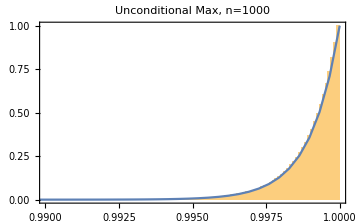

```mathematica
Show[Histogram[maxs,{10^-4},"CDF",PlotRange->{{0.990,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Unconditional Max, n=1000"],
Plot[cdfordk[x,1000,1000],{x,0,1},ImageSize->Medium,PlotRange->{{0.990,1},All},Frame->True,PlotLabel->"Unconditional Max, n=1000"]]
```

```mathematica
fmax2[list_]:=Max[Complement[list,{Max[list]}]];
```

```mathematica
max2s=Map[fmax2,draws];
```

General::munfl: Exp[-10794.7] is too small to represent as a normalized machine number; precision may be lost.

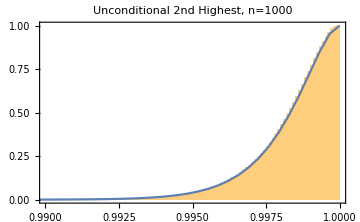

```mathematica
Show[Histogram[max2s,{10^-4},"CDF",PlotRange->{{0.990,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Unconditional 2nd Highest, n=1000"],
Plot[cdfordk[x,1000,1000-1],{x,0,1},ImageSize->Medium,PlotRange->{{0.990,1},All},Frame->True,PlotLabel->"Unconditional 2nd Highest, n=1000"]]
```

```mathematica
maxs990=Map[Max[Take[#,-10]]&,draws];
```

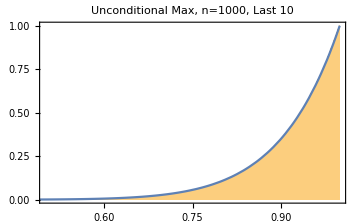

```mathematica
Show[Histogram[maxs990,{10^-3},"CDF",PlotRange->{{0.50,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Unconditional Max, n=1000, Last 10"],
Plot[cdfordk[x,10,10],{x,0,1},ImageSize->Medium,PlotRange->{{0.50,1},All},Frame->True,PlotLabel->"Unconditional Max, n=1000, Last 10"]]
```

```mathematica
max2s990=Map[fmax2[Take[#,-10]]&,draws];
```

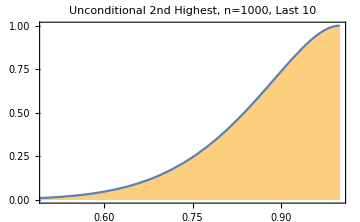

```mathematica
Show[Histogram[max2s990,{10^-3},"CDF",PlotRange->{{0.50,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Unconditional 2nd Highest, n=1000, Last 10"],
Plot[cdfordk[x,10,10-1],{x,0,1},ImageSize->Medium,PlotRange->{{0.50,1},All},Frame->True,PlotLabel->"Unconditional 2nd Highest, n=1000, Last 10"]]
```

```mathematica
maxs990cond=Map[If[Max[Take[#,-10]]==Max[#],{Max[#]},{}]&,draws];
```

```mathematica
Take[maxs990cond,50]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{0.998092},{},{},{},{},{},{},{},{},{},{},{},{},{},{0.999652},{},{},{},{},{},{},{},{},{}}

```mathematica
Flatten[Take[maxs990cond,50]]
```

{0.998092,0.999652}

General::munfl: 0.0000204286^1000. is too small to represent as a normalized machine number; precision may be lost.

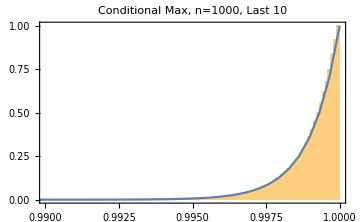

```mathematica
Show[Histogram[Flatten[maxs990cond],{10^-4},"CDF",PlotRange->{{0.990,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Conditional Max, n=1000, Last 10"],
Plot[cdfordk[x,1000,1000],{x,0,1},ImageSize->Medium,PlotRange->{{0.990,1},All},Frame->True,PlotLabel->"Conditional Max, n=1000, Last 10"]]
```

```mathematica
max2s990cond=Map[If[Max[Take[#,-10]]==Max[#],{fmax2[#]},{}]&,draws];
```

General::munfl: Exp[-10794.7] is too small to represent as a normalized machine number; precision may be lost.

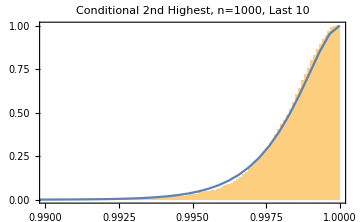

```mathematica
Show[Histogram[Flatten[max2s990cond],{10^-4},"CDF",PlotRange->{{0.990,1},All},Frame->True,ImageSize->Medium,PlotLabel->"Conditional 2nd Highest, n=1000, Last 10"],
Plot[cdfordk[x,1000,1000-1],{x,0,1},ImageSize->Medium,PlotRange->{{0.990,1},All},Frame->True,PlotLabel->"Conditional 2nd Highest, n=1000, Last 10"]]
```